```mathematica
f[x_]:=0.01*(((1-epsilon)*(-(q+epsilon-epsilon*R)+√((q+epsilon-epsilon*R)^2+4R*epsilon*q)))/(2R))
```

```mathematica
f[x]
```

(0.005 (1-epsilon) (-epsilon-q+epsilon R+√(4 epsilon q R+(epsilon+q-epsilon R)^2)))/R

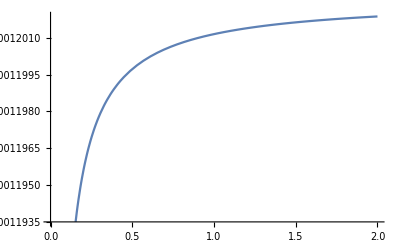

```mathematica
Plot[f[x],{q,0,2}]
```

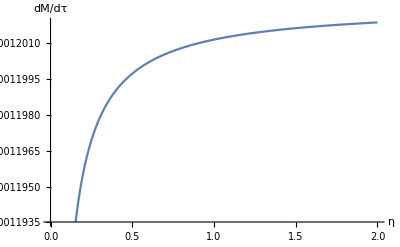

```mathematica
Show[%124,AxesLabel->{HoldForm[η],HoldForm[dM/dτ]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Desktop\\M_at_EE.pdf",%125,"PDF"]
```

C:\Users\Roger Zhang\Desktop\M_at_EE.pdf

```mathematica
epsilon=11/9136
```

11/9136

```mathematica
R=4.5
```

4.5

```mathematica
g[x_]:=0.005 (1-epsilon) (-epsilon-q+epsilon R+√(4 epsilon q R+(epsilon+q-epsilon R)^2))
```

```mathematica
g[x]
```

0.00499398 (0.0042141+√((-0.0042141+q)^2+0.0216725 q)-q)

```mathematica
Simplify[0.004993979859894922 (0.004214098073555167+√((-0.004214098073555167+q)^2+0.021672504378283712 q)-q)]
```

0.0000210451-0.00499398 q+0.00499398 √(0.0000177586+0.0132443 q+q^2)